```mathematica
y=2009;
```

```mathematica
dowJonesMember={"MMM","AXP","AAPL","BA","CAT","CVX","CSCO","KO","DD","XOM","GE","GS","HD","INTC","IBM","JNJ","JPM","MCD","MRK","MSFT","NKE","PFE","PG","TRV","UNH","UTX","VZ","WMT","DIS"};
```

```mathematica
stocksSets=splitup[dowJonesMember,5];
Length/@stocksSets
```

{5,6,6,6,6}

```mathematica
trainingSets=Flatten[Drop[stocksSets,{#}]]&/@Range[Length[stocksSets]];
testSets=stocksSets[[#]]&/@Range[Length[stocksSets]];
```

```mathematica
trainingSet=x[2005,2012]/@dowJonesMember;
```

```mathematica
trainingSets=splitup[trainingSet,5];
```

```mathematica
trainingSets=Function[n,
Flatten[Drop[trainingSets,{n}],2]]/@Range[Length[trainingSets]];
```

```mathematica
Dimensions/@trainingSets
```

{{42288,64},{40526,64},{40526,64},{40526,64},{40526,64}}

```mathematica
{Φs,As,bs}=Transpose[Φ/@trainingSets];
```

```mathematica
trainingReturns=r[2005,2012]/@dowJonesMember;
```

```mathematica
trainingReturns=splitup[testReturns,5];
```

```mathematica
trainingReturns=Function[n,
Flatten[Drop[trainingReturns,{n}]]]/@Range[Length[trainingReturns]];
```

```mathematica
Dimensions/@trainingReturns
```

{{42288},{40526},{40526},{40526},{40526}}

```mathematica
qs=MapThread[findQ[0,1,#1,#2]&,{Φs,trainingReturns}];
```

```mathematica
Norm/@qs
```

{1.,1.,1.,1.,1.}

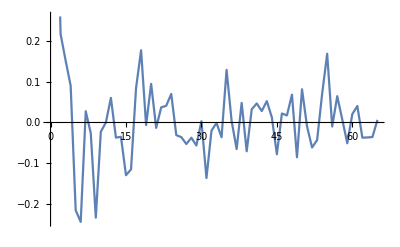

```mathematica
ListLinePlot[qs[[1]]]
```

```mathematica
q=findQ[0,1,trainingSets[[1]],trainingReturns[[1]]];
```

>>  
Calling SDPT3 4.0: 66 variables, 1 equality constraints
------------------------------------------------------------

 num. of constraints =  1
 dim. of socp   var  = 65,   num. of socp blk  =  1
 dim. of linear var  =  1
*******************************************************************
   SDPT3: Infeasible path-following algorithms
*******************************************************************
 version  predcorr  gam  expon  scale_data
    NT      1      0.000   1        0    
it pstep dstep pinfeas dinfeas  gap      prim-obj      dual-obj    cputime
-------------------------------------------------------------------
 0|0.000|0.000|8.5e+00|1.4e+00|4.4e+09| 0.000000e+00  0.000000e+00| 0:0:00| chol  1  1 
 1|0.384|0.473|5.4e+00|7.5e-01|1.6e+09|-3.344148e+09 -6.796502e+05| 0:0:00| chol  1  1 
 2|0.001|1.000|5.3e+00|2.6e-11|3.0e+11| 7.861020e+08 -2.530740e+10| 0:0:00| chol  1  1 
 3|1.000|1.000|3.9e-08|2.6e-12|2.1e+10| 6.397125e+07 -2.115618e+10| 0:0:00| chol  1  1 
 4|1.000|0.959|6.8e-09|2.6e-09|8.7e+08| 5.694656e+07 -8.169203e+08| 0:0:00| chol  1  1 
 5|1.000|0.492|1.4e-10|2.7e-09|2.8e+08|-2.781966e+08 -5.588639e+08| 0:0:00| chol  1  1 
 6|0.911|1.000|2.8e-11|2.9e-11|2.5e+07|-5.257738e+08 -5.506755e+08| 0:0:00| chol  1  1 
 7|0.986|0.986|2.2e-11|6.0e-12|3.4e+05|-5.400035e+08 -5.403466e+08| 0:0:00| chol  1  1 
 8|0.989|0.989|7.8e-12|4.5e-12|3.8e+03|-5.402004e+08 -5.402042e+08| 0:0:00| chol  1  1 
 9|0.989|0.989|2.6e-12|1.6e-12|4.2e+01|-5.402025e+08 -5.402026e+08| 0:0:00| chol  1  1 
10|0.989|0.989|2.9e-14|1.0e-12|4.6e-01|-5.402026e+08 -5.402026e+08| 0:0:00|
  stop: max(relative gap, infeasibilities) < 1.49e-08
-------------------------------------------------------------------
 number of iterations   = 10
 primal objective value = -5.40202565e+08
 dual   objective value = -5.40202566e+08
 gap := trace(XZ)       = 4.58e-01
 relative gap           = 4.24e-10
 actual relative gap    = 4.24e-10
 rel. primal infeas (scaled problem)   = 2.85e-14
 rel. dual     "        "       "      = 1.02e-12
 rel. primal infeas (unscaled problem) = 0.00e+00
 rel. dual     "        "       "      = 0.00e+00
 norm(X), norm(y), norm(Z) = 1.4e+00, 5.4e+08, 9.4e+08
 norm(A), norm(b), norm(C) = 2.4e+00, 2.0e+00, 5.4e+08
 Total CPU time (secs)  = 0.11  
 CPU time per iteration = 0.01  
 termination code       =  0
 DIMACS: 2.9e-14  0.0e+00  1.0e-12  0.0e+00  4.2e-10  4.2e-10
-------------------------------------------------------------------
 
------------------------------------------------------------
Status: Solved
Optimal value (cvx_optval): +5.40203e+08

```mathematica
Norm[q]
```

1.

```mathematica
q
```

{2.06984×10^-8,1.80658×10^-8,1.53788×10^-8,8.44069×10^-10,-6.17925×10^-10,2.34648×10^-9,-2.048×10^-10,-1.02714×10^-8,-8.27795×10^-11,1.0535×10^-9,3.98497×10^-9,-7.23636×10^-10,-7.36787×10^-10,-5.1944×10^-9,-4.47751×10^-9,5.14191×10^-9,9.59019×10^-9,7.47587×10^-10,5.62548×10^-9,4.03524×10^-10,2.83399×10^-9,3.05066×10^-9,4.46396×10^-9,-4.07694×10^-10,-6.45398×10^-10,-1.45897×10^-9,-8.51496×10^-10,-1.68698×10^-9,1.21465×10^-9,-5.49202×10^-9,1.17483×10^-10,8.95013×10^-10,-7.05885×10^-10,7.29236×10^-9,1.26753×10^-9,-2.0547×10^-9,3.40771×10^-9,-2.31892×10^-9,2.64369×10^-9,3.33921×10^-9,2.32261×10^-9,3.54968×10^-9,1.67626×10^-9,-2.67508×10^-9,2.14978×10^-9,1.92418×10^-9,4.37878×10^-9,-3.02759×10^-9,5.01372×10^-9,6.1746×10^-10,-1.8735×10^-9,-1.08868×10^-9,4.39407×10^-9,9.18854×10^-9,6.02731×10^-10,4.17324×10^-9,1.30507×10^-9,9.08417×10^-7,1.03874×10^-8,1.15985×10^-8,1.08186×10^-6,1.09453×10^-6,1.1044×10^-6,1.}

```mathematica
Dimensions/@{trainingSets[[1]],trainingReturns[[1]]}
```

{{42288,64},{42288}}

```mathematica
magic[5]
```

{{17,24,1,8,15},{23,5,7,14,16},{4,6,13,20,22},{10,12,19,21,3},{11,18,25,2,9}}

```mathematica
trainingSet//Dimensions
```

{29,1762,64}

```mathematica
Flatten[Drop[trainingSet,#],1]&/@Range[
```

```mathematica
Module[
{training,A,b,index,testFeatures,normalizedTestFeatures,trainingReturns,testReturns},

index=ToString[#];
{training,A,b}=Φ[x[y]/@trainingSets[[#]]];
exportFeatures[training,"features_fold"<>index<>".csv"];

testFeatures=Flatten[x[y]/@testSets[[#]],1];
normalizedTestFeatures=Φ[testFeatures,A,b];
exportFeatures[normalizedTestFeatures,"testFeatures_fold"<>index<>".csv"];

trainingReturns=Flatten[r[y]/@trainingSets[[#]],1];
exportReturns[trainingReturns,"returns_fold"<>index<>".csv"];

testReturns=Transpose[r[y]/@testSets[[#]]];
exportFeatures[testReturns,"testReturns_fold"<>index<>".csv"]
]&/@Range[2,5]
```

Calling financial features feeds for MMM

Calling financial features feeds for AXP

Calling financial features feeds for AAPL

Calling financial features feeds for BA

Calling financial features feeds for CAT

Calling financial features feeds for GE

Calling financial features feeds for GS

Calling financial features feeds for HD

Calling financial features feeds for INTC

Calling financial features feeds for IBM

Calling financial features feeds for JNJ

Calling financial features feeds for JPM

Calling financial features feeds for MCD

Calling financial features feeds for MRK

Calling financial features feeds for MSFT

Calling financial features feeds for NKE

Calling financial features feeds for PFE

Calling financial features feeds for PG

Calling financial features feeds for TRV

Calling financial features feeds for UNH

Calling financial features feeds for UTX

Calling financial features feeds for VZ

Calling financial features feeds for V

Calling financial features feeds for WMT

Calling financial features feeds for DIS

Calling financial features feeds for CVX

Calling financial features feeds for CSCO

Calling financial features feeds for KO

Calling financial features feeds for DD

Calling financial features feeds for XOM

Calling returns values for MMM

Calling returns values for AXP

Calling returns values for AAPL

Calling returns values for BA

Calling returns values for CAT

Calling returns values for GE

Calling returns values for GS

Calling returns values for HD

Calling returns values for INTC

Calling returns values for IBM

Calling returns values for JNJ

Calling returns values for JPM

Calling returns values for MCD

Calling returns values for MRK

Calling returns values for MSFT

Calling returns values for NKE

Calling returns values for PFE

Calling returns values for PG

Calling returns values for TRV

Calling returns values for UNH

Calling returns values for UTX

Calling returns values for VZ

Calling returns values for V

Calling returns values for WMT

Calling returns values for DIS

Calling returns values for CVX

Calling returns values for CSCO

Calling returns values for KO

Calling returns values for DD

Calling returns values for XOM

Calling financial features feeds for MMM

Calling financial features feeds for AXP

Calling financial features feeds for AAPL

Calling financial features feeds for BA

Calling financial features feeds for CAT

Calling financial features feeds for CVX

Calling financial features feeds for CSCO

Calling financial features feeds for KO

Calling financial features feeds for DD

Calling financial features feeds for XOM

Calling financial features feeds for JNJ

Calling financial features feeds for JPM

Calling financial features feeds for MCD

Calling financial features feeds for MRK

Calling financial features feeds for MSFT

Calling financial features feeds for NKE

Calling financial features feeds for PFE

Calling financial features feeds for PG

Calling financial features feeds for TRV

Calling financial features feeds for UNH

Calling financial features feeds for UTX

Calling financial features feeds for VZ

Calling financial features feeds for V

Calling financial features feeds for WMT

Calling financial features feeds for DIS

Calling financial features feeds for GE

Calling financial features feeds for GS

Calling financial features feeds for HD

Calling financial features feeds for INTC

Calling financial features feeds for IBM

Calling returns values for MMM

Calling returns values for AXP

Calling returns values for AAPL

Calling returns values for BA

Calling returns values for CAT

Calling returns values for CVX

Calling returns values for CSCO

Calling returns values for KO

Calling returns values for DD

Calling returns values for XOM

Calling returns values for JNJ

Calling returns values for JPM

Calling returns values for MCD

Calling returns values for MRK

Calling returns values for MSFT

Calling returns values for NKE

Calling returns values for PFE

Calling returns values for PG

Calling returns values for TRV

Calling returns values for UNH

Calling returns values for UTX

Calling returns values for VZ

Calling returns values for V

Calling returns values for WMT

Calling returns values for DIS

Calling returns values for GE

Calling returns values for GS

Calling returns values for HD

Calling returns values for INTC

Calling returns values for IBM

Calling financial features feeds for MMM

Calling financial features feeds for AXP

Calling financial features feeds for AAPL

Calling financial features feeds for BA

Calling financial features feeds for CAT

Calling financial features feeds for CVX

Calling financial features feeds for CSCO

Calling financial features feeds for KO

Calling financial features feeds for DD

Calling financial features feeds for XOM

Calling financial features feeds for GE

Calling financial features feeds for GS

Calling financial features feeds for HD

Calling financial features feeds for INTC

Calling financial features feeds for IBM

Calling financial features feeds for NKE

Calling financial features feeds for PFE

Calling financial features feeds for PG

Calling financial features feeds for TRV

Calling financial features feeds for UNH

Calling financial features feeds for UTX

Calling financial features feeds for VZ

Calling financial features feeds for V

Calling financial features feeds for WMT

Calling financial features feeds for DIS

Calling financial features feeds for JNJ

Calling financial features feeds for JPM

Calling financial features feeds for MCD

Calling financial features feeds for MRK

Calling financial features feeds for MSFT

Calling returns values for MMM

Calling returns values for AXP

Calling returns values for AAPL

Calling returns values for BA

Calling returns values for CAT

Calling returns values for CVX

Calling returns values for CSCO

Calling returns values for KO

Calling returns values for DD

Calling returns values for XOM

Calling returns values for GE

Calling returns values for GS

Calling returns values for HD

Calling returns values for INTC

Calling returns values for IBM

Calling returns values for NKE

Calling returns values for PFE

Calling returns values for PG

Calling returns values for TRV

Calling returns values for UNH

Calling returns values for UTX

Calling returns values for VZ

Calling returns values for V

Calling returns values for WMT

Calling returns values for DIS

Calling returns values for JNJ

Calling returns values for JPM

Calling returns values for MCD

Calling returns values for MRK

Calling returns values for MSFT

Calling financial features feeds for MMM

Calling financial features feeds for AXP

Calling financial features feeds for AAPL

Calling financial features feeds for BA

Calling financial features feeds for CAT

Calling financial features feeds for CVX

Calling financial features feeds for CSCO

Calling financial features feeds for KO

Calling financial features feeds for DD

Calling financial features feeds for XOM

Calling financial features feeds for GE

Calling financial features feeds for GS

Calling financial features feeds for HD

Calling financial features feeds for INTC

Calling financial features feeds for IBM

Calling financial features feeds for JNJ

Calling financial features feeds for JPM

Calling financial features feeds for MCD

Calling financial features feeds for MRK

Calling financial features feeds for MSFT

Calling financial features feeds for UTX

Calling financial features feeds for VZ

Calling financial features feeds for V

Calling financial features feeds for WMT

Calling financial features feeds for DIS

Calling financial features feeds for NKE

Calling financial features feeds for PFE

Calling financial features feeds for PG

Calling financial features feeds for TRV

Calling financial features feeds for UNH

Calling returns values for MMM

Calling returns values for AXP

Calling returns values for AAPL

Calling returns values for BA

Calling returns values for CAT

Calling returns values for CVX

Calling returns values for CSCO

Calling returns values for KO

Calling returns values for DD

Calling returns values for XOM

Calling returns values for GE

Calling returns values for GS

Calling returns values for HD

Calling returns values for INTC

Calling returns values for IBM

Calling returns values for JNJ

Calling returns values for JPM

Calling returns values for MCD

Calling returns values for MRK

Calling returns values for MSFT

Calling returns values for UTX

Calling returns values for VZ

Calling returns values for V

Calling returns values for WMT

Calling returns values for DIS

Calling returns values for NKE

Calling returns values for PFE

Calling returns values for PG

Calling returns values for TRV

Calling returns values for UNH

{/Users/TBM/Desktop/ProjetC/Data/testReturns_fold2.csv,/Users/TBM/Desktop/ProjetC/Data/testReturns_fold3.csv,/Users/TBM/Desktop/ProjetC/Data/testReturns_fold4.csv,/Users/TBM/Desktop/ProjetC/Data/testReturns_fold5.csv}

```mathematica
FinancialData["AAPL","Volatility50Day",{2010}]
```

{0.264664,0.266803,0.266313,0.268491,0.261546,0.254294,0.251842,0.234208,0.235742,0.236156,0.239118,0.25502,0.258129,0.249209,0.274652,0.28142,0.282821,0.282295,0.297219,0.30827,0.3101,0.304697,0.307213,0.310493,0.31317,0.313461,0.312104,0.312242,0.313216,0.31365,0.315375,0.313159,0.308269,0.308652,0.295043,0.297178,0.299187,0.298405,0.297669,0.30105,0.298269,0.295758,0.294523,0.305656,0.305255,0.298517,0.297876,0.296329,0.295434,0.296785,0.294984,0.29503,0.292422,0.293615,0.294247,0.29517,0.29365,0.293984,0.295999,0.29291,0.278849,0.276245,0.27253,0.243342,0.2376,0.236331,0.236255,0.212073,0.189865,0.188917,0.189971,0.18881,0.164967,0.163053,0.164414,0.203878,0.20812,0.207629,0.209112,0.221865,0.221382,0.226442,0.237959,0.238724,0.246384,0.247256,0.26637,0.286144,0.326214,0.326305,0.328611,0.331356,0.325323,0.325292,0.324291,0.326725,0.342657,0.344968,0.345556,0.346056,0.346278,0.355471,0.355051,0.355666,0.355014,0.355265,0.360412,0.361921,0.362214,0.365698,0.371395,0.372123,0.37154,0.374178,0.379139,0.380475,0.380506,0.38243,0.383264,0.383543,0.383239,0.383539,0.383611,0.397943,0.377527,0.372676,0.370563,0.371014,0.377387,0.3774,0.372567,0.367517,0.367569,0.361906,0.361333,0.350533,0.33847,0.298857,0.29875,0.297731,0.296044,0.293226,0.296021,0.296853,0.29557,0.277423,0.277018,0.274356,0.273874,0.273914,0.261586,0.260135,0.258662,0.269695,0.270178,0.264073,0.260608,0.263217,0.25685,0.249763,0.248229,0.250465,0.25085,0.243072,0.239789,0.239276,0.238107,0.235577,0.245493,0.245955,0.252905,0.252533,0.233786,0.229696,0.227681,0.228752,0.228493,0.211476,0.217301,0.217432,0.22448,0.217775,0.219316,0.218603,0.218492,0.213901,0.211735,0.211184,0.210565,0.210993,0.213719,0.224756,0.222518,0.220509,0.222459,0.219779,0.22051,0.220573,0.220096,0.234731,0.235119,0.243807,0.225747,0.226363,0.22513,0.223894,0.222452,0.222718,0.221255,0.224786,0.220764,0.212393,0.2122,0.210675,0.211734,0.211697,0.213825,0.206532,0.207502,0.214134,0.214048,0.216178,0.216613,0.222942,0.222464,0.226406,0.229772,0.228164,0.227642,0.220077,0.224938,0.225815,0.225911,0.224968,0.225099,0.222518,0.223025,0.220816,0.220257,0.216961,0.203284,0.20331,0.203264,0.200666,0.200712,0.199912,0.199756,0.199855,0.178519,0.177168,0.165286,0.165755,0.165774,0.171296,0.171375,0.171785,0.171792,0.170614,0.170615,0.169976,0.167182,0.165959,0.162775,0.171674,0.172187,0.176647,0.18145,0.19481,0.18429,0.18422,0.178478,0.185832,0.17837,0.180583,0.175396,0.171376,0.1674,0.170117,0.17069,0.164409,0.163816,0.163931,0.163849,0.163265,0.162727,0.16611,0.174369,0.193059,0.194503,0.194078,0.19659,0.198681,0.200691,0.201065,0.205473,0.205474,0.207732,0.207713,0.209241,0.213241,0.215027,0.214783,0.217283,0.241357,0.242745,0.244256,0.250755,0.247431,0.247733,0.250062,0.253574,0.253055,0.247477,0.247663,0.243775,0.241498,0.231595,0.230592,0.230026,0.230001,0.225934,0.226627,0.223474,0.225075,0.226317,0.227518,0.226767,0.229677,0.231043,0.236744,0.236755,0.236775,0.236704,0.236563,0.235979,0.232088,0.218272,0.216879,0.217733,0.214927,0.212409,0.211296,0.210953,0.205185,0.208674,0.212018,0.213115,0.214026,0.210925,0.210588,0.210232,0.204343,0.17865,0.176318,0.174833,0.17865,0.178988,0.178443,0.175205,0.173161,0.177397,0.177341,0.176899,0.180558,0.179216,0.183017,0.186412,0.186607,0.18942,0.191429,0.203096,0.203524,0.21093,0.212104,0.213039,0.212022,0.208156,0.20612,0.20518,0.208751,0.208647,0.211485,0.21067,0.212987,0.211396,0.212719,0.212594,0.216069,0.22224,0.222729,0.229534,0.228717,0.230435,0.226783,0.220376,0.231065,0.230621,0.23106,0.228885,0.234623,0.23395,0.252054,0.253021,0.285252,0.305551,0.312281,0.317845,0.317515,0.316585,0.313948,0.313978,0.327526,0.331685,0.331688,0.345447,0.342566,0.342787,0.344153,0.342426,0.336854,0.337983,0.335156,0.336267,0.335808,0.335964,0.335679,0.338788,0.335777,0.334641,0.33527,0.334298,0.336353,0.338427,0.338326,0.337999,0.343942,0.341699,0.338049,0.338651,0.333918,0.336101,0.338585,0.339244,0.337927,0.334781,0.334789,0.337656,0.35517,0.358405,0.357963,0.347258,0.353206,0.326622,0.302125,0.32441,0.319842,0.31977,0.32569,0.328602,0.32889,0.316404,0.308825,0.308885,0.295623,0.295344,0.296247,0.291345,0.289111,0.29127,0.296527,0.301603,0.298517,0.298384,0.302727,0.303706,0.304287,0.304264,0.304891,0.307214,0.311421,0.308293,0.311893,0.311836,0.317309,0.31456,0.314398,0.315048,0.314522,0.314452,0.312417,0.307863,0.305154,0.305433,0.308043,0.30809,0.304676,0.282401,0.286133,0.285925,0.283925,0.274947,0.275517,0.275893,0.24317,0.242347,0.244118,0.233346,0.229743,0.230325,0.229433,0.229516,0.229569,0.224289,0.22456,0.223855,0.224017,0.224178,0.225562,0.218873,0.213737,0.251699,0.249227,0.244228,0.243238,0.23768,0.23669,0.232649,0.230146,0.219894,0.217778,0.209143,0.21722,0.2134,0.214394,0.215204,0.224804,0.223779,0.222956,0.22742,0.228314,0.227161,0.225402,0.215567,0.215887,0.216279,0.216222,0.206561,0.216388,0.217951,0.217776,0.220536,0.217605,0.218068,0.223331,0.232914,0.235096,0.235455,0.239379,0.238518,0.240227,0.241067,0.24174,0.241695,0.241762,0.241736,0.244851,0.244577,0.249726,0.244305,0.214906,0.21402,0.214125,0.21822,0.219439,0.220536,0.233596,0.257618,0.276945,0.277269,0.290587,0.289648,0.289842,0.292268,0.346693,0.341458,0.342297,0.351711,0.348267,0.348104,0.348696,0.355141,0.355225,0.353243,0.352184,0.352141,0.352567,0.350464,0.350909,0.352294,0.355577,0.355286,0.377226,0.371833,0.366069,0.36632,0.366467,0.363653,0.364276,0.364126,0.369732,0.36996,0.367264,0.367904,0.367618,0.368577,0.368322,0.361408,0.359026,0.358757,0.35699,0.360261,0.359548,0.359529,0.360535,0.355598,0.345244,0.325324,0.325564,0.316694,0.317229,0.318765,0.315949,0.25289,0.253203,0.254298,0.244101,0.244463,0.245108,0.245425,0.235639,0.235246,0.235168,0.236707,0.240188,0.239544,0.236974,0.257635,0.255694,0.248288,0.250485,0.223909,0.223656,0.217586,0.217765,0.218135,0.215388,0.214178,0.214204,0.201865,0.203265,0.202946,0.20094,0.201454,0.202718,0.205153,0.208289,0.210386,0.212118,0.21215,0.211553,0.211778,0.211662,0.211867,0.211593,0.206678,0.208045,0.20843,0.206339,0.210832,0.209446,0.210035,0.210872,0.210925,0.2107,0.208843,0.20785,0.206728,0.206134,0.209477,0.21885,0.221265,0.225441,0.227694,0.229734,0.229217,0.204634,0.205805,0.210384,0.21494,0.207541,0.207418,0.213009,0.211189,0.210498,0.216664,0.217549,0.221734,0.237118,0.251558,0.262531,0.262904,0.263285,0.260114,0.253846,0.252615,0.257712,0.259953,0.259832,0.267832,0.278091,0.282373,0.281516,0.281331,0.278441,0.280937,0.279861,0.326277,0.322252,0.32243,0.323486,0.328754,0.327104,0.325121,0.326466,0.326442,0.326638,0.327975,0.35691,0.356729,0.359659,0.353617,0.356684,0.356267,0.357173,0.362293,0.366038,0.371794,0.370157,0.370324,0.369304,0.367654,0.368062,0.367486,0.36215,0.378189,0.38474,0.377416,0.369563,0.363271,0.362958,0.36355,0.364984,0.364076,0.371782,0.371119,0.382564,0.382666,0.373505,0.365605,0.36587,0.470694,0.472779,0.476325,0.477158,0.476905,0.446347,0.446245,0.448528,0.454642,0.447217,0.453928,0.455912,0.455813,0.458334,0.458163,0.457194,0.43453,0.432435,0.432069,0.432062,0.429431,0.430654,0.431333,0.423963,0.421463,0.417762,0.419682,0.425213,0.425702,0.426966,0.426549,0.428091,0.42985,0.416094,0.409255,0.414486,0.416361,0.416301,0.416144,0.415192,0.417023,0.417153,0.409719,0.405871,0.396344,0.401659,0.401794,0.401202,0.398456,0.266631,0.261995,0.256657,0.257324,0.257323,0.258202,0.263066,0.259817,0.276695,0.28221,0.272107,0.27466,0.277449,0.27276,0.273713,0.279104,0.287444,0.295591,0.290952,0.292472,0.292355,0.294162,0.292831,0.292846,0.2931,0.287745,0.281581,0.281881,0.291421,0.291808,0.291856,0.294386,0.290482,0.290564,0.289846,0.284469,0.278309,0.278913,0.280735,0.280879,0.277071,0.276985,0.277514,0.275978,0.272395,0.26289,0.26299,0.264384,0.264029,0.264788,0.264515,0.264503,0.264592,0.266489,0.266076,0.267731,0.265227,0.233451,0.226416,0.226718,0.233051,0.234764,0.234941,0.235343,0.230751,0.223483,0.213088,0.215636,0.213017,0.211688,0.204739,0.204632,0.2029,0.204908,0.204546,0.207388,0.231977,0.218319,0.216649,0.219143,0.215211,0.214503,0.215258,0.216979,0.218879,0.219023,0.218476,0.216176,0.218565,0.227374,0.249491,0.250746,0.247618,0.24776,0.247433,0.24984,0.247308,0.247019,0.24453,0.244517,0.255119,0.249438,0.246033,0.246319,0.236108,0.238821,0.237461,0.234771,0.236031,0.236432,0.26899,0.269544,0.271992,0.282605,0.281194,0.284042,0.284243,0.285541,0.304394,0.304593,0.307385,0.307821,0.305701,0.307645,0.307735,0.288005,0.289591,0.289547,0.288475,0.289672,0.29052,0.290202,0.289277,0.287867,0.28702,0.287074,0.287173,0.285102,0.283428,0.264485,0.262365,0.263733,0.26467,0.264137,0.268861,0.271023,0.271268,0.271396,0.272694,0.263891,0.263962,0.266975,0.267956,0.26812,0.264446,0.26382,0.265312,0.263655,0.259607,0.22348,0.224011,0.22096,0.206201,0.205548,0.20468,0.207672,0.208108,0.182236,0.19,0.18547,0.184942,0.187589,0.184925,0.179597,0.181188,0.177893,0.180548,0.179969,0.176529,0.177,0.17967,0.179951,0.196827,0.197421,0.198505,0.199365,0.2007,0.195311,0.19833,0.204405,0.202685,0.201646,0.201466,0.194976,0.192609,0.192606,0.196899,0.199724,0.200157,0.208514,0.207286,0.204795,0.205222,0.210048,0.210661,0.282618,0.283399,0.282219,0.282213,0.281653,0.282293,0.282818,0.282592,0.281249,0.27908,0.277463,0.276828,0.272104,0.272078,0.271936,0.272469,0.272103,0.273042,0.272982,0.273798,0.273481,0.277221,0.277131,0.276829,0.276172,0.2755,0.260976,0.260893,0.260635,0.261429,0.260579,0.260108,0.259427,0.254915,0.255435,0.254946,0.254701,0.253731,0.254638,0.255489,0.252535,0.248399,0.248136,0.241687,0.239988,0.239791,0.239418,0.237635,0.239325,0.144548,0.14435,0.147779,0.149018,0.149169,0.146953,0.146119,0.147735,0.146811,0.141251,0.141124,0.228477,0.226443,0.241416,0.241615,0.238529,0.236457,0.234428,0.235863,0.236011,0.234897,0.231776,0.231967,0.233089,0.232905,0.232958,0.233958,0.235541,0.236433,0.235953,0.235924,0.233777,0.23219,0.234744,0.234846,0.237014,0.236821,0.237851,0.238318,0.238426,0.236474,0.23622,0.237482,0.237288,0.237788,0.242435,0.243539,0.240878,0.2368,0.236702,0.236491,0.235584,0.234369,0.235532,0.23423,0.234209,0.234282,0.234051,0.233975,0.23073,0.154236,0.158896,0.138793,0.138306,0.138279,0.138287,0.140224,0.141556,0.139461,0.146357,0.148662,0.148918,0.147757,0.157021,0.157235,0.155266,0.154918,0.155039,0.155357,0.168641,0.168825,0.168364,0.164437,0.164338,0.159705,0.159387,0.160601,0.15797,0.158627,0.158541,0.158495,0.156854,0.159064,0.158563,0.152802,0.150337,0.14925,0.150305,0.152072,0.151526,0.148654,0.148901,0.180706,0.182197,0.182617,0.182016,0.181234,0.192568,0.192593,0.192363,0.187448,0.18771,0.188168,0.187807,0.189084,0.187188,0.187594,0.188336,0.204939,0.212478,0.212686,0.212407,0.208185,0.208674,0.208371,0.206111,0.206567,0.211562,0.202152,0.202112,0.202885,0.204179,0.206293,0.208671,0.211074,0.214345,0.222293,0.220789,0.223936,0.223856,0.222588,0.223113,0.223324,0.223562,0.223923,0.225452,0.225632,0.224279,0.224306,0.224318,0.223918,0.199527,0.199781,0.200996,0.200974,0.200652,0.192029,0.193268,0.195049,0.194945,0.196513,0.198216,0.19919,0.197633,0.214172,0.212601,0.211977,0.189551,0.180833,0.188909,0.190916,0.192832,0.192919,0.197581,0.200775,0.202466,0.204654,0.213897,0.214802,0.213925,0.212204,0.210055,0.209233,0.207876,0.206552,0.204525,0.205911,0.213181,0.21304,0.215241,0.228814,0.228571,0.23584,0.235715,0.234148,0.241885,0.242404,0.249331,0.249849,0.256445,0.256104,0.254215,0.264905,0.292242,0.300242,0.300966,0.301732,0.300108,0.30055,0.298115,0.298074,0.297249,0.300288,0.294248,0.294965,0.294275,0.2941,0.293915,0.288268,0.28712,0.287628,0.288121,0.292104,0.290103,0.290558,0.286577,0.280326,0.280066,0.283014,0.28269,0.282222,0.285041,0.288686,0.28923,0.285796,0.285078,0.277268,0.277647,0.277875,0.268655,0.269222,0.262045,0.2701,0.269906,0.261986,0.265423,0.264022,0.263961,0.258927,0.260736,0.262409,0.247701,0.216815,0.206502,0.203253,0.202151,0.202206,0.202173,0.203648,0.208353,0.208569,0.206416,0.200704,0.19906,0.20274}